Define the earth with North pointing upwards. Define a  curve on the sphere at fixed  lattitude rotating at constant angular velocity. 

Next define a rotation matrix.  1) Tilt the earth’s north pole in the x-direction. 2) add a time dependent precession in the x-y plane.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ryanplestid/Research/Physics_Projects/Archived_Projects/Solar-Upscatter-Dipole/Mathematica/PaperI-clean

```mathematica
Nhat={0,0,1};
p= {r Cos[Ωt] ,r Sin[Ωt],z};
Rtilt[θtilt_]:={{Cos[θtilt],0,Sin[θtilt]},{0,1,0},{-Sin[θtilt],0,Cos[θtilt]}}; 
Rprec[ωt_]:= {{Cos[ωt],Sin[ωt],0},{-Sin[ωt],Cos[ωt],0},{0,0,1}};
```

{Cos[ωt] Sin[θtilt],-Sin[θtilt] Sin[ωt],Cos[θtilt]}

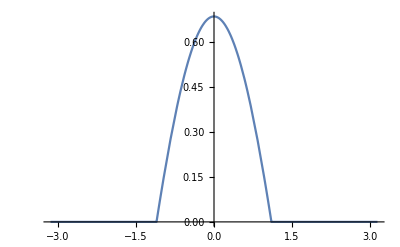

```mathematica
Rprec[ωt].Rtilt[θtilt].Nhat//Simplify
p′=(Rprec[ωt].Rtilt[θtilt].p);
p′Shift=p′+{-d,0,0};
dSolved=d/.Solve[p′Shift.p′Shift==R^2,d]/.Ωt->Ωt+ ωt;
dSolved/. ωt-> 182(2π)/365/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/.z->Cos[42.28/360 2π]/. R-> 1;
Plot[{%⟦2⟧},{Ωt,-π,π},PlotRange->Full]
```

```mathematica
(dSolved/. θtilt-> π/4//Simplify)/. ωt-> π//Simplify
```

{-(z-r Cos[Ωt]+√(2 R^2-z^2-2 r z Cos[Ωt]-r^2 Cos[Ωt]^2-2 r^2 Sin[Ωt]^2))/(√2),(-z+r Cos[Ωt]+√(2 R^2-z^2-2 r z Cos[Ωt]-r^2 Cos[Ωt]^2-2 r^2 Sin[Ωt]^2))/(√2)}

We can calculate a ``universal function’’ for each day of the year

```mathematica
UnivTabs=Table[{ωt,Interpolation@Table[{x,1/(2π)NIntegrate[1-Exp[-x (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[42.28/360 2π] R/.R-> 1)],{Ωt,-π,π}]},{x,Table[0.001*1.5^n,{n,1,33}]}]},{ωt,Table[(2π)/365 n,{n,0,364,1}]} ]//Quiet//FullSimplify;
```

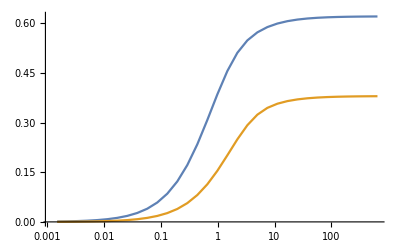

```mathematica
ListLogLinearPlot[{UnivTabs⟦1⟧⟦2⟧,UnivTabs⟦192⟧⟦2⟧},Joined->True]
```

```mathematica
UnivTabsYearBorexino=Table[{x,1/(2π)1/(2π)NIntegrate[1-Exp[-x (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[42.28/360 2π] R/.R-> 1)],{Ωt,-π,π},{ωt,-π,π}]},{x,Table[0.0001*1.5^n,{n,1,40}]}]//Quiet//FullSimplify;
UnivTabsYearSK=Table[{x,1/(2π)1/(2π)NIntegrate[1-Exp[-x (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[36.42/360 2π] R/.R-> 1)],{Ωt,-π,π},{ωt,-π,π}]},{x,Table[0.0001*1.5^n,{n,1,40}]}]//Quiet//FullSimplify;
UnivTabsYearArctic=Table[{x,1/(2π)1/(2π)NIntegrate[1-Exp[-x (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[66.5/360 2π] R/.R-> 1)],{Ωt,-π,π},{ωt,-π,π}]},{x,Table[0.0001*1.5^n,{n,1,40}]}]//Quiet//FullSimplify;
UnivTabsYearEquator=Table[{x,1/(2π)1/(2π)NIntegrate[1-Exp[-x (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[0/360 2π] R/.R-> 1)],{Ωt,-π,π},{ωt,-π,π}]},{x,Table[0.0001*1.5^n,{n,1,40}]}]//Quiet//FullSimplify;
```

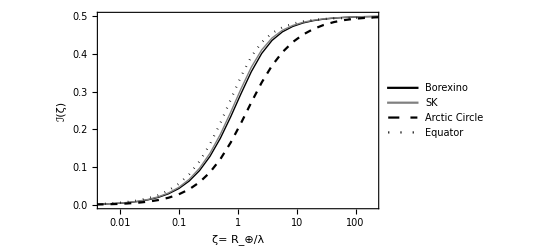

```mathematica
fig=ListLogLinearPlot[{UnivTabsYearBorexino,UnivTabsYearSK,UnivTabsYearArctic,UnivTabsYearEquator},Joined->True,PlotRange->{{0.005,200},Full},PlotStyle->{{Black,Thick},{Gray,Thick},{Black,Dashed},{Black,Dotted}},PlotLegends->Placed[{"Borexino","SK","Arctic Circle","Equator"},{0.2,0.7}],Frame-> True,FrameStyle->Black,FrameLabel->(Style[#,13]&)/@{"ζ= R_⊕/λ","ℐ(ζ)"}]
```

```mathematica
Export["PDFs/I-of-zeta.pdf",fig];
```

```mathematica
AvgLTabsBorexino=Table[{365/(2π) ωt,1/(2π)NIntegrate[ (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[42.28/360 2π] R/.R-> 1),{Ωt,-π,π}]},{ωt,Table[(2π)/365 n,{n,0,364,1}]} ]//Quiet//FullSimplify;
AvgLTabSK=Table[{365/(2π) ωt,1/(2π)NIntegrate[ (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[36.42/360 2π] R/.R-> 1),{Ωt,-π,π}]},{ωt,Table[(2π)/365 n,{n,0,364,1}]} ]//Quiet//FullSimplify;
AvgLTabsArctic=Table[{365/(2π) ωt,1/(2π)NIntegrate[ (dSolved⟦2⟧/.θtilt-> 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[42.28/360 2π] R/.R-> 1),{Ωt,-π,π}]},{ωt,Table[(2π)/365 n,{n,0,364,1}]} ]//Quiet//FullSimplify;
AvgLTabEquator=Table[{365/(2π) ωt,1/(2π)NIntegrate[ (dSolved⟦2⟧/.θtilt->0 22.25/360 2π/.r->  √(R^2-z^2)/. z->Sin[0/360 2π] R/.R-> 1),{Ωt,-π,π}]},{ωt,Table[(2π)/365 n,{n,0,364,1}]} ]//Quiet//FullSimplify;
```

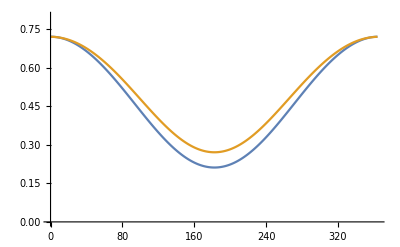

```mathematica
ListPlot[{AvgLTabsBorexino,AvgLTabSK},Joined->True,PlotRange-> {0,0.8}]
```

```mathematica
Integrate[dSolved⟦2⟧/.θtilt-> 0//FullSimplify,Ωt]
```

((2 R^2-2 z^2) √((r^2 cos(2 Ωt)-r^2+2 R^2-2 z^2)/(2 R^2-2 z^2)) Ωt(2 r^2)/(2 R^2-2 z^2))/(√2 √(r^2 cos(2 Ωt)-r^2+2 R^2-2 z^2))+r sin(Ωt)

```mathematica
1/(2π)(%/. Ωt->  2π)/. z-> 0/. r->  R
```

(2 √(R^2))/π

```mathematica
EllipticE[0]
```

π/2

```mathematica
w
```

```mathematica
Mean[AvgLTabEquator]
```

{182,0.63662}

```mathematica
Export["Earth-Geo/L-avg-Borexino.m",AvgLTabsBorexino];
Export["Earth-Geo/L-avg-SK.m",AvgLTabSK];
```

```mathematica
Export["Earth-Geo/I-year-SK.m",UnivTabsYearSK];
Export["Earth-Geo/I-year-Borexino.m",UnivTabsYearBorexino];
```

```mathematica
Nhat={0,0,1};
p= {r Cos[Ωt] ,r Sin[Ωt],z};
Rtilt[θtilt_]:={{Cos[θtilt],0,Sin[θtilt]},{0,1,0},{-Sin[θtilt],0,Cos[θtilt]}}; 
Rprec[ωt_]:= {{Cos[ωt],Sin[ωt],0},{-Sin[ωt],Cos[ωt],0},{0,0,1}};

Rprec[ωt].Rtilt[θtilt].Nhat//Simplify
p′=(Rprec[ωt].Rtilt[θtilt].p);
p′Shift=p′+{-x,0,0};
testReal=If[(# ∈Reals&)[#],#,0]&;
x/.  Solve[r1==p′Shift.p′Shift/. r-> √(1-z^2)/.r1-> 0.5/. θtilt-> 23.5/360 2π,x];
Lcore=(%⟦2⟧-%⟦1⟧//Simplify)/. z->  Sin[42.5/360 2π];
LcoreAvg=1/(4 π^2)NIntegrate[testReal[Lcore],{ωt,0,2π},{Ωt,0,2π}];
x/.  Solve[r1==p′Shift.p′Shift/. r-> √(1-z^2)/.r1-> 1/. θtilt-> 23.5/360 2π,x];
LSlab=(%⟦2⟧-%⟦1⟧//Simplify)/. z->Sin[42.5/360 2π];
LSlabAvg=1/(4 π^2)NIntegrate[testReal[LSlab],{ωt,0,2π},{Ωt,0,2π}];
```

{Cos[ωt] Sin[θtilt],-Sin[θtilt] Sin[ωt],Cos[θtilt]}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.31601 and 0.000460343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
(LSlabAvg-LcoreAvg)/LSlabAvg
LcoreAvg/LSlabAvg
```

0.801582

0.198418

```mathematica
(1-1/8)4 + 1/8 13//N
```

5.125